## 能带论

### （1）高能情况: E>V_0

### 通过周期性边界条件求得的关于 A, B, C, D 的关系的矩阵

```mathematica
Clear["Global`*"]
{{1,1,-1,-1},{α,-α,-β,β},{Exp[ⅈ (δ-α b)],Exp[ⅈ (δ+α b)],-Exp[ⅈ β a],-Exp[-ⅈ β a]},{α Exp[ⅈ (δ-α b)],-α Exp[ⅈ (δ+α b)],-β Exp[ⅈ β a],β Exp[-ⅈ β a]}}//MatrixForm
```

(1 | 1 | -1 | -1
α | -α | -β | β
ⅇ^(ⅈ (-b α+δ)) | ⅇ^(ⅈ (b α+δ)) | -ⅇ^(ⅈ a β) | -ⅇ^(-ⅈ a β)
ⅇ^(ⅈ (-b α+δ)) α | -ⅇ^(ⅈ (b α+δ)) α | -ⅇ^(ⅈ a β) β | ⅇ^(-ⅈ a β) β)

### 展开此矩阵的行列式，两边同处以 4αβ，得到

```mathematica
Det[{{1,1,-1,-1},{α,-α,-β,β},{Exp[ⅈ (δ-α b)],Exp[ⅈ (δ+α b)],-Exp[ⅈ β a],-Exp[-ⅈ β a]},{α Exp[ⅈ (δ-α b)],-α Exp[ⅈ (δ+α b)],-β Exp[ⅈ β a],β Exp[-ⅈ β a]}}]/(4 α β)==0//FullSimplify
```

(ⅇ^(ⅈ δ) (2 α β (-Cos[b α] Cos[a β]+Cos[δ])+(α^2+β^2) Sin[b α] Sin[a β]))/(α β)==0

### 行列式为0，找出 Cos[δ] 对于 a,b, α, β 的关系。 这是 E>V_0 情况下周期势场中电子能量E所满足的超越方程。

```mathematica
Solve[(ⅇ^(ⅈ δ) (2 α β (-Cos[b α] Cos[a β]+Cos[δ])+(α^2+β^2) Sin[b α] Sin[a β]))/(α β)==0,Cos[δ]]//FullSimplify
```

{{Cos[δ]→Cos[b α] Cos[a β]-((α^2+β^2) Sin[b α] Sin[a β])/(2 α β)}}

### 假设势井宽度 b 很小 Cos[b α]~1; Sin[b α]~b α;

```mathematica
1 Cos[a β]-((α^2+β^2) b α Sin[a β])/(2 α β)
```

Cos[a β]-(b (α^2+β^2) Sin[a β])/(2 β)

### 上下同时乘以 a ,变形为 Cos[a β]-(a b (α^2+β^2) Sin[a β])/(2 (β a)),令 a β = θ，并带入 α, β 的定义式

```mathematica
Cos[θ]-(a b (α^2+β^2) Sin[θ])/(2 θ)
```

Cos[θ]-(a b (α^2+β^2) Sin[θ])/(2 θ)

```mathematica
α[EE_]:=√((2m)/ℏ^2(EE-V0));
β[EE_]:=√((2m)/ℏ^2 EE);
Cos[θ]-(a b ((α[e])^2+(β[e])^2) Sin[θ])/(2 θ)//FullSimplify
```

Cos[θ]+(a b m (-2 e+V0) Sin[θ])/(θ ℏ^2)

### 假定 V0->E

```mathematica
Cos[θ]+(a b m (-V0) Sin[θ])/(θ ℏ^2)
```

Cos[θ]-(a b m V0 Sin[θ])/(θ ℏ^2)

### 作出上式的图像。 考虑到 Cos[δ] 的取值范围在 -1 到 1 之间。

```mathematica
Plot[{Cos[θ]-(3π)/2*Sin[θ]/θ,1,-1},{θ,-4π,4π},PlotRange->{{-4π,4π},{3,-6}}]
```

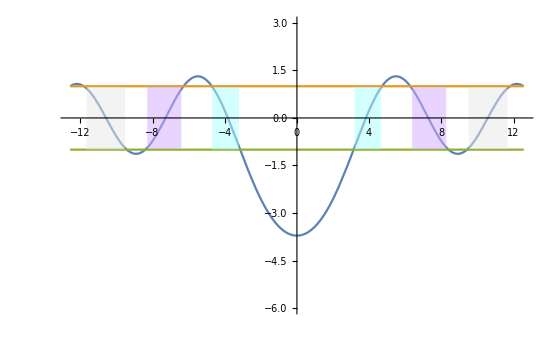

### （2）低能情况： E<V_0

#### 当 E<V_0 ，E-V_0<0 ，所以 α 为虚数。令 α^2=(ⅈ ρ)^2 ，其中 ρ 是实数。 将超越方程（transcendental equation）中的 α 全部替换为 ⅈ ρ，则有

```mathematica
Solve[(ⅇ^(ⅈ δ) (2 (ⅈ ρ) β (-Cos[b (ⅈ ρ)] Cos[a β]+Cos[δ])+((ⅈ ρ)^2+β^2) Sin[b (ⅈ ρ)] Sin[a β]))/((ⅈ ρ) β)==0,Cos[δ]]//FullSimplify
```

{{Cos[δ]→Cos[a β] Cosh[b ρ]+((-β^2+ρ^2) Sin[a β] Sinh[b ρ])/(2 β ρ)}}

#### 依旧假设势井宽度 b 很小 Cosh[b ρ]~1; Sinh[b ρ]~b ρ;

```mathematica
Cos[a β] *1+((-β^2+ρ^2) Sin[a β] *(b ρ))/(2 β ρ)
```

Cos[a β]+(b (-β^2+ρ^2) Sin[a β])/(2 β)

#### 上下同时乘以 a ,变形为 Cos[a β]+(ab (-β^2+ρ^2) Sin[a β])/(2a β),令 a β = ϕ，并带入 ρ, β 的定义式

```mathematica
ρ[EE_]:=√((2m)/ℏ^2(V0-EE));
β[EE_]:=√((2m)/ℏ^2 EE);
Cos[ϕ]+(ab (-β[e]^2+ρ[e]^2) Sin[ϕ])/(2ϕ)//FullSimplify
```

Cos[ϕ]+(ab m (-2 e+V0) Sin[ϕ])/(ϕ ℏ^2)

#### 假定 V_0>>e,以至 V_0-2E~V_0

```mathematica
Cos[ϕ]+(ab m (V0) Sin[ϕ])/(ϕ ℏ^2)
```

Cos[ϕ]+(ab m V0 Sin[ϕ])/(ϕ ℏ^2)

#### 作出上式的图像。 考虑到 Cos[δ] 的取值范围在 -1 到 1 之间。

```mathematica
Plot[{Cos[ϕ]+Sin[ϕ]/ϕ*(3π)/2,1,-1},{ϕ,-4π,4π},PlotRange->{{-4π,4π},{-3,6}}]
```

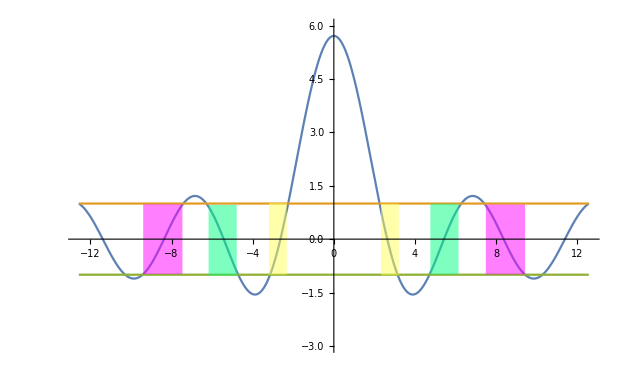

#### 对比两种能量 E>V_0 和 E<V_0 下的 Cos[δ]: Cos[θ]-(a b m V0 Sin[θ])/(θ ℏ^2) E>V_0 Cos[ϕ]+(ab m V0 Sin[ϕ])/(ϕ ℏ^2) E<V_0 对于自由电子模型，V_0=0，所以 Cos[δ] = β a, β 是自由电子的波数 对于非自由电子模型，V_0≠0，所以 Cos[δ] = k a = Cos[β a]±(a b m (-2 e+V0) Sin[β a])/(β a ℏ^2)，k是周期性势场中电子波的波数

```mathematica
Clear["Global`*"]
```

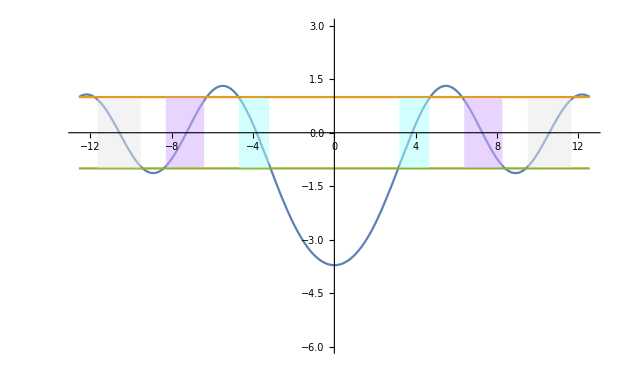
```mathematica
p1=-Graphics-;
p2=-Graphics-;
Show[p1,p2]
```

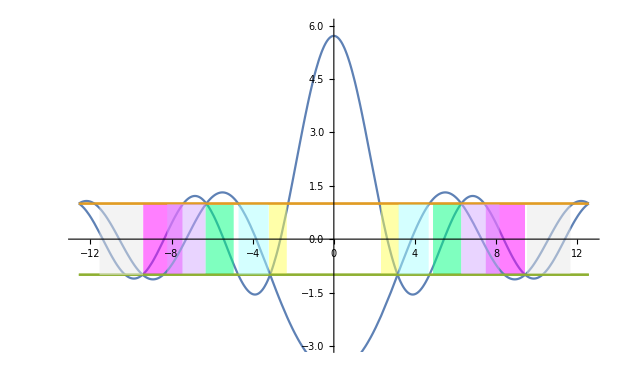

#### 二者的第 n 个能带在 nπ 处相连接。